## Helper Functions

#### Distances

```mathematica
SpacerDistance[numberOfElements_,spacer_,outerSpacersQ_:False]:=
spacer(numberOfElements-If[outerSpacersQ,-1,1]);

ElementDistance[numberOfElements_,girth_]:=
girth numberOfElements;

SpacedElementDistance[numberOfElements_, girth_,spacer_,outerSpacersQ_:False]:=
ElementDistance[numberOfElements,girth]+
SpacerDistance[numberOfElements,spacer,outerSpacersQ]

ElementsSize[elements_,girth_:1,spacer_:1,orientation_:Up,outerSpacersQ_:False ]:=
With[
{
max = Max@elements,(* only works with positive integers and 0 *)
distance=SpacedElementDistance[Length@elements, girth, spacer, outerSpacersQ]
},
If[
HorizontalQ@orientation,
{distance,max},
{max,distance}
]
]
```

#### Ticks

```mathematica
ClearAll[MakeTicks]
Options[MakeTicks]={ReversedQ->False,Max-> 1,Min->0};
MakeTicks[numberOfTicks_,OptionsPattern[]]:=
With[
{
maxValue=OptionValue[Max],
minValue=OptionValue[Min],
ReversedQ=OptionValue[ReversedQ]
},
With[
{
nTicks=If[numberOfTicks===Automatic,Min[{5, Abs@maxValue}],numberOfTicks]
},
Join[
{If[ReversedQ,{-minValue,minValue},{minValue,minValue}]},
With[
{partition=(maxValue-minValue)/If[(nTicks-1)===0,0.000000000001,(nTicks-1)]},
Table[
{
If[ReversedQ,
-(partition*i+minValue),
partition*i+minValue
],

If[ReversedQ,
partition*i+minValue,
(partition*i+minValue)]
},
{i,nTicks-1}
]
]
]
]
]
```

#### Orientation

```mathematica
(* Helpers for determining orientation *)
HorizontalQ[orientation_]:=MemberQ[{Down,Up},orientation];
VerticalQ[orientation_]:=MemberQ[{Left,Right},orientation];
```

#### Text Size

```mathematica
TextDimensions[text_]:=ImageDimensions[ImageCrop[Graphics[text]]]
```

## Bar Chart

#### Coordinates

```mathematica
(* Get the bar coordinates *)
BarCoordinates[value_,girth_:1,orientation_:Up, opt:OptionsPattern[]]:=
With[
{hQ=HorizontalQ@orientation,vQ=VerticalQ@orientation},
{{0,0},
{
If[vQ,If[orientation===Left, -value, value],girth],
If[hQ,If[orientation===Down, -value, value],girth]
}
}
]
```

#### Translate

```mathematica
(* Translate the bar over by the other bars in the same chart and spacers therein *)
BarTranslate[index_,girth_,orientation_,spacer_,outerSpacersQ:False]:=
With[
{
hQ=HorizontalQ@orientation,
distance=SpacedElementDistance[index, girth, spacer, outerSpacersQ]-girth
},

If[
HorizontalQ@orientation,
{distance, 0},
{0,distance}
]
]
```

#### Bar

```mathematica
(* Make a bar *)
Options[Bar]={
Orientation->Left,
Girth->1,
Spacer->1,
OuterSpacersQ->False
};
Bar[value_, index_, opt: OptionsPattern[]]:=
Module[
{
girth=OptionValue[Girth],
orientation=OptionValue[Orientation],
spacer=OptionValue[Spacer]
},
Translate[
Rectangle@@BarCoordinates[value, girth,orientation],
BarTranslate[index, girth, orientation, spacer, OptionValue[OuterSpacersQ]]
]
]
```

#### Wrapped Bar Chart

```mathematica
(* Wrapper for making all the bars *)
Options[UpSetBarChartHelper]=Options[Bar];
UpSetBarChartHelper[data_, opt: OptionsPattern[]]:=
Module[
{

},
Table[Bar[data[[i]], i, opt],{i,Length[data]}]
]
```

#### Inset Size calculator

```mathematica
(* If inset size is automatic, and we want perfect measurement, then clear to have it in a helper function*)
ClearAll[BarChartInsetSize]
BarChartInsetSize[data_,insetSize_, girth_, spacer_, orientation_,outerSpacersQ_:False]:=
With[
{
size=ElementsSize[data,girth, spacer,orientation,outerSpacersQ],
hQ=HorizontalQ@orientation
},
If[insetSize===Automatic,size,insetSize]
]
```

#### Bar Chart

```mathematica
(* Generic bar chart *)
Options[UpSetBarChart]=Join[{
Translate->{0,0}, (* Translate all bars *)
InsetPosition->{0,0},(* Inset position of all bars *)
InsetOffsetPosition->{0,0}, (* Inset offset position of all bars *)
InsetSize->Automatic, (* Inset size of all bars *)
NumberOfTicks->Automatic, (* Number of ticks in axis *)
AxesQ->True (* yes or no to axes *)
},
Options[UpSetBarChartHelper] (* and whatever the helper func can use *)
];

UpSetBarChart[data_,opt: OptionsPattern[]]:=
Module[
{
translate=OptionValue[Translate],
insetPosition=OptionValue["InsetPosition"],
insetOffsetPosition=OptionValue["InsetOffsetPosition"],
insetSize=BarChartInsetSize[
data,
OptionValue[InsetSize],
OptionValue[Girth],
OptionValue[Spacer],
OptionValue[Orientation]
],
orientation=OptionValue[Orientation],
ticks=MakeTicks[OptionValue[NumberOfTicks],Max->Max@data,Min->0,ReversedQ->MemberQ[{Down, Left},OptionValue[Orientation]]],
options= FilterRules[{opt},Options[UpSetBarChartHelper]]
},
Inset[
Graphics[
Translate[
UpSetBarChartHelper[data,options],
translate
],
Axes->If[OptionValue[AxesQ],
{!HorizontalQ@orientation,! VerticalQ@orientation},
{False, False}
]
,
Ticks->If[!HorizontalQ@orientation,{ticks, {}},{{},ticks}]
],
insetPosition,
insetOffsetPosition,
insetSize
]
]
```

#### Test

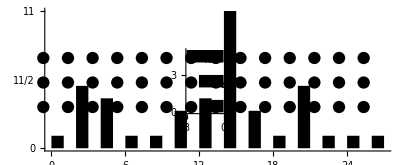

```mathematica
text={"my", "very","fun", "labels"};
text={"my", "very","fun"};
a={1,2,3};
(*text=ToString/@a;*)
b={1,5,4,1};
(*b={1,5,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1};*)
(*b={1,5,4,1,1,3,4,11,3,1,5,1,1,1};*)

spacer=1; (* space between bars *)
girth=1; (* width / height of bars depending on orientation*)
textSpace=1; (* how much coordinate space shoudl be preserved for text *)
axes=False; (* yes / no axes*)
(*axes=True;*)
With[
{
barsLeft =UpSetBarChart[a,Translate->{0,0},InsetPosition->{0,0},InsetOffsetPosition->{0,0},InsetSize->Automatic,Orientation->Left,Girth->girth,Spacer->spacer,AxesQ->axes],

barsUp=UpSetBarChart[
b,Translate->{0,0},InsetPosition->{0,0},
InsetOffsetPosition->{
(-2spacer-textSpace),
-(spacer+Last@ElementsSize[a, girth, spacer,Left,False])
},
InsetSize->Automatic,Orientation->Up,Girth->girth,Spacer->spacer,AxesQ->axes
],

radius=girth/2,
td=TextDimensions[Text/@text],
aElementsSize=ElementsSize[a, girth, spacer,Left,False],
bElementsSize=ElementsSize[b, girth, spacer,Up,False]
},


Graphics[
{
(* Set Cardinalities *)
barsLeft,
(* Comparison Cardinalities *)
barsUp,
(* Set Labels *)
Inset[
Graphics[
Table[
Translate[
Text[
text[[i]],
{0,0},(* move via translate *)
{-1,0} (* text aligned left and bottom *)
],
{
0, (* moving vertically only *)
SpacedElementDistance[i,girth,spacer,False]-girth
}
]
,{i, Length@text}
]
],
{0,0},
{-spacer ,- girth / 3 2 (*2/3*)},
{5(*this is arbitrary sort of*),SpacedElementDistance[Length@text,girth,spacer,False]-girth}
],

(* Indicator Grid *)
Inset[
Graphics[
Table[
Disk[
{
i-radius+SpacerDistance[i,spacer],
j-radius+SpacerDistance[j,spacer]
},
radius
],{i,Length@b},{j,Length@a}
]
],
{0,0},
{ -2spacer-textSpace,0},
{
First@bElementsSize,
Last@aElementsSize
}
]
},
(* End of Graphics List*)

PlotRange->{
{
-(Max@a),
2spacer+textSpace+First@bElementsSize
},
{
-2,
spacer+Last@aElementsSize+Max@b
}
}
]
]
```